# Integration Rules for ∫(sin^j(z))^m(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1∧a^2=b^2

Domain Map

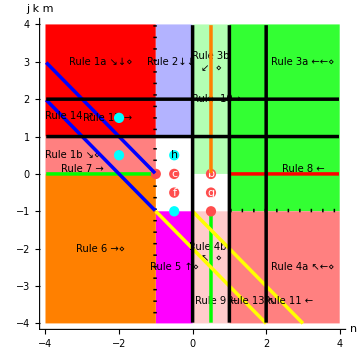

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

# Integration Rules for ∫(a+b sin^k(z))^n ⅆz when k^2=1∧a^2=b^2

Rule a:  ∫1/(a+b Sin[c+d x]^k)ⅆx

#### Reference: G&R 2.555.3', CRC 337', A&S 4.3.134'/5'

#### Derivation: Rule 1b with m=0, k=1 and n=-1

#### Rule a1: If a^2-b^2=0, then

∫1/(a+b Sin[c+d x])ⅆx  ⟶  -Cos[c+d x]/(d (b+a Sin[c+d x]))

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  -Cos[c+d*x]/(d*(b+a*Sin[c+d*x])) /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

#### Reference: G&R 2.555.4', CRC 338'/9', A&S 4.3.134'/5'

```mathematica
Int[1/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  Sin[c+d*x]/(d*(b+a*Cos[c+d*x])) /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Basis: 1/(a+b z)=1/a-(b z)/(a(a+b z))

#### Note: The rule for integrands of the same form when a^2-b^2≠0 could subsume this rule, but the resulting antiderivative will look less like the integrand involving sines instead of cosecants.

#### Rule a2: If a^2-b^2=0, then

∫1/(a+b Csc[c+d x])ⅆx  ⟶  x/a-b/a∫Csc[c+d x]/(a+b Csc[c+d x])ⅆx

#### Program code:

```mathematica
Int[1/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  x/a - Dist[b/a,Int[1/(sin[c+d*x]*(a+b/sin[c+d*x])),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

Rule b:  ∫√(a+b Sin[c+d x]^k)ⅆx

#### Derivation: Rule 3b with m=0, k=1 and n=1/2

#### Rule b1: If a^2-b^2=0, then

∫√(a+b Sin[c+d x])ⅆx  ⟶  -(2 b Cos[c+d x])/(d √(a+b Sin[c+d x]))

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  -2*b*Cos[c+d*x]/(d*Sqrt[a+b*Sin[c+d*x]]) /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

```mathematica
Int[Sqrt[a_+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  2*b*Sin[c+d*x]/(d*Sqrt[a+b*Cos[c+d*x]]) /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

#### Author: Martin on sci.math.symbolic on 10 March 2011

#### Rule b2: If a^2-b^2=0, then

∫√(a+b Csc[c+d x])ⅆx  ⟶  -(2 √a)/dArcTan[(√a Cot[c+d x])/(√(a+b Csc[c+d x]))]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*Sqrt[a]/d*ArcTan[(Sqrt[a]*Cot[c+d*x])/Sqrt[a+b*Csc[c+d*x]]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

Rule c:  ∫1/(√(a+b Sin[c+d x]))ⅆx

#### Note: Although not essential, this rule produces a simpler antiderivative than rule c3.

#### Rule c1: If a-b=0, then

∫1/(√(a+b Cos[c+d x]))ⅆx  ⟶  2/(d √(a+b Cos[c+d x]))Cos[(c+d x)/2]ArcTanh[Sin[(c+d x)/2]]

#### Program code:

```mathematica
Int[1/Sqrt[a_+b_.*sin[c_.+Pi/2+d_.*x_]],x_Symbol] :=
  2/(d*Sqrt[a+b*Cos[c+d*x]])*Cos[(c+d*x)/2]*ArcTanh[Sin[(c+d*x)/2]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a-b]
```

#### Note: Although not essential, this rule produces a simpler antiderivative than rule c3.

#### Rule c2: If a+b=0, then

∫1/(√(a+b Cos[c+d x]))ⅆx  ⟶  -2/(d √(a+b Cos[c+d x]))Sin[(c+d x)/2]ArcTanh[Cos[(c+d x)/2]]

#### Program code:

```mathematica
Int[1/Sqrt[a_+b_.*sin[c_.+Pi/2+d_.*x_]],x_Symbol] :=
  -2/(d*Sqrt[a+b*Cos[c+d*x]])*Sin[(c+d*x)/2]*ArcTanh[Cos[(c+d*x)/2]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a+b]
```

#### Rule c3: If a^2-b^2=0, then

∫1/(√(a+b Sin[c+d x]))ⅆx  ⟶  2/(d √(a+b Sin[c+d x]))Cos[(c+d x)/2-(π b)/(4a)]ArcTanh[Sin[(c+d x)/2-(π b)/(4a)]]

#### Program code:

```mathematica
Int[1/Sqrt[a_+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  2/(d*Sqrt[a+b*Sin[c+d*x]])*Cos[(c+d*x)/2-Pi*b/(4*a)]*ArcTanh[Sin[(c+d*x)/2-Pi*b/(4*a)]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

Rules 15-16:  ∫(a+b Csc[c+d x])^n ⅆx

#### Derivation: Rule 6 with m=0 and k=-1

#### Rule 15: If a^2-b^2=0 ∧ n<-1, then

∫(a+b Csc[c+d x])^n ⅆx  ⟶  -(Cot[c+d x](a+b Csc[c+d x])^n)/(d (2n+1))+
1/(a^2(2n+1)) ∫(a(2n+1)-b(n+1)Csc[c+d x])(a+b Csc[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),Int[(a*(2*n+1)-(b*(n+1))*sin[c+d*x]^(-1))*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Derivation: Rule 3a with m=0 and k=-1

#### Rule 16: If a^2-b^2=0 ∧ n>1 ∧ n≠2, then

∫(a+b Csc[c+d x])^n ⅆx  ⟶  -(b^2 Cot[c+d x](a+b Csc[c+d x])^(n-2))/(d(n-1))+
a/(n-1)∫(a (n-1)+b (3 n-4)Csc[c+d x]) (a+b Csc[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -b^2*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n-2)/(d*(n-1)) + 
  Dist[a/(n-1),Int[(a*(n-1)+(b*(3*n-4))*sin[c+d*x]^(-1))*(a+b*sin[c+d*x]^(-1))^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n>1 && n≠2
```

# Integration Rules for ∫(sin^j(z))^m(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1∧a^2=b^2

Rule d:  ∫(√(a+b Sin[c+d x]))/Sin[c+d x]ⅆx

#### Derivation: Piecewise constant extraction and trig substitution

#### Basis: If a-b=0, then ∂_z Cos[z/2]/(√(a+b Cos[z]))=0

#### Basis: If a-b=0, then a+b Cos[z]=2 a Cos[z/2]^2

#### Note: Although not essential, this rule produces a simpler antiderivative than rule d3.

#### Rule d1: If a-b=0, then

∫(√(a+b Cos[c+d x]))/Cos[c+d x]ⅆx  ⟶  (2a Cos[(c+d x)/2])/(√(a+b Cos[c+d x]))∫Cos[(c+d x)/2]/Cos[c+d x]ⅆx                                         
                                 ⟶  (2 √2 b  Cos[(c+d x)/2])/(d √(a+b Cos[c+d x]))ArcTanh[√2 Sin[(c+d x)/2]]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+Pi/2+d_.*x_]]/sin[c_.+Pi/2+d_.*x_],x_Symbol] :=
  2*Sqrt[2]*b*Cos[(c+d*x)/2]/(d*Sqrt[a+b*Cos[c+d*x]])*ArcTanh[Sqrt[2]*Sin[(c+d*x)/2]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a-b]
```

#### Derivation: Piecewise constant extraction and trig substitution

#### Basis: If a+b=0, then ∂_z Sin[z/2]/(√(a+b Cos[z]))=0

#### Basis: If a+b=0, then a+b Cos[z]=2 a Sin[z/2]^2

#### Note: Although not essential, this rule produces a simpler antiderivative than rule d3.

#### Rule d2: If a+b=0, then

∫(√(a+b Cos[c+d x]))/Cos[c+d x]ⅆx  ⟶  (2a Sin[(c+d x)/2])/(√(a+b Cos[c+d x]))∫Sin[(c+d x)/2]/Cos[c+d x]ⅆx                                           
                                ⟶  (2 √2 a  Sin[(c+d x)/2])/(d √(a+b Cos[c+d x]))ArcTanh[√2 Cos[(c+d x)/2]]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+Pi/2+d_.*x_]]/sin[c_.+Pi/2+d_.*x_],x_Symbol] :=
  2*Sqrt[2]*a*Sin[(c+d*x)/2]/(d*Sqrt[a+b*Cos[c+d*x]])*ArcTanh[Sqrt[2]*Cos[(c+d*x)/2]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a+b]
```

#### Derivation: Piecewise constant extraction and trig substitution

#### Rule d3: If a^2-b^2=0, then

∫(√(a+b Sin[c+d x]))/Sin[c+d x]ⅆx  ⟶  (2 √2 b  Cos[(c+d x)/2-(π b)/(4a)])/(d √(a+b Sin[c+d x]))ArcTanh[√2 Sin[(c+d x)/2-(π b)/(4a)]]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]]/sin[c_.+d_.*x_],x_Symbol] :=
  2*Sqrt[2]*b*Cos[(c+d*x)/2-Pi*b/(4*a)]/(d*Sqrt[a+b*Sin[c+d*x]])*
    ArcTanh[Sqrt[2]*Sin[(c+d*x)/2-Pi*b/(4*a)]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

Rule e:    ∫1/(Sin[c+d x]^((k+1)/2)√(a+b Sin[c+d x]^k))ⅆx

#### Author: Martin on sci.math.symbolic on 10 March 2011

#### Derivation: Algebraic expansion

#### Basis: If k^2=1, then 1/(z^((k+1)/2) √(a+b z^k))=(√(a+b z^k))/(a z^((k+1)/2))-(b z^((k-1)/2))/(a √(a+b z^k))

#### Rule e: If k^2=1 ∧ a^2-b^2=0, then

∫1/(Sin[c+d x]^((k+1)/2)√(a+b Sin[c+d x]^k))ⅆx  ⟶  1/a∫(√(a+b Sin[c+d x]^k))/Sin[c+d x]^((k+1)/2)ⅆx-b/a∫Sin[c+d x]^((k-1)/2)/(√(a+b Sin[c+d x]^k))ⅆx

#### Program code:

```mathematica
Int[1/(sin[c_.+d_.*x_]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[1/a,Int[Sqrt[a+b*sin[c+d*x]]/sin[c+d*x],x]] - 
  Dist[b/a,Int[1/Sqrt[a+b*sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

```mathematica
Int[1/Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  1/a*Int[Sqrt[a+b*sin[c+d*x]^(-1)],x] - 
  b/a*Int[sin[c+d*x]^(-1)/Sqrt[a+b*sin[c+d*x]^(-1)],x] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

Rule f:  ∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx

#### Basis: z0=z

#### Note: This is a special case of the rule for a^2≠b^2.

#### Rule f1: If a-b=0 ∧ a>0, then

∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx  ⟶  (√2)/(d √a)ArcSin[Tan[(c+dx)/2-π/4]]

#### Program code:

```mathematica
Int[1/(Sqrt[sin[c_.+Pi/2+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+Pi/2+d_.*x_]]),x_Symbol] :=
  Sqrt[2]/(d*Sqrt[a])*ArcSin[Tan[(c+d*x)/2]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a-b] && PositiveQ[a]
```

```mathematica
Int[1/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Sqrt[2]/(d*Sqrt[a])*ArcSin[Tan[(c+d*x)/2-Pi/4]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a-b] && PositiveQ[a]
```

#### Author: Martin 10 March 2011

#### Derivation: ???

#### Rule f2: If a^2-b^2=0, then

∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx  ⟶  -(√2 √b)/(a d)ArcTan[(√b Cos[c+d x])/(√2 √Sin[c+d x] √(a+b Sin[c+d x]))]

#### Program code:

```mathematica
Int[1/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  -Sqrt[2]*Sqrt[b]/(a*d)*ArcTan[Sqrt[b]*Cos[c+d*x]/(Sqrt[2]*Sqrt[Sin[c+d*x]]*Sqrt[a+b*Sin[c+d*x]])] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && Not[ZeroQ[a-b] && PositiveQ[a]]
```

Rule g:  ∫(√(a+b Sin[c+d x]))/(√Sin[c+d x])ⅆx

#### Author: Martin 10 March 2011

#### Derivation: ???

#### Rule g: If a^2-b^2=0, then

∫(√(a+b Sin[c+d x]))/(√Sin[c+d x])ⅆx  ⟶  -(2 √b)/dArcTan[(√b Cos[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*sin[c_.+d_.*x_]]/Sqrt[sin[c_.+d_.*x_]],x_Symbol] :=
  -2*Sqrt[b]/d*ArcTan[Sqrt[b]*Cos[c+d*x]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Sin[c+d*x]])] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

Rule h:    ∫(√Sin[c+d x])/(√(a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: (√z)/(√(a+b z))=(√(a+b z))/(b √z)-a/(b √z √(a+b z))

#### Rule h: If a^2-b^2=0, then

∫(√Sin[c+d x])/(√(a+b Sin[c+d x]))ⅆx  ⟶  1/b∫(√(a+b Sin[c+d x]))/(√Sin[c+d x])ⅆx-a/b∫1/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]]/Sqrt[a_+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  Dist[1/b,Int[Sqrt[a+b*sin[c+d*x]]/Sqrt[sin[c+d*x]],x]] - 
  Dist[a/b,Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

Rule i:  ∫((Sin[c+d x]^j)^(m/2))/((a+b Sin[c+d x]^k)^2)ⅆx

#### Derivation: Rule 1b with n=-2 and 2j k m+k-2=0

#### Rule i: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ 2j k m+k-2=0, then

∫((Sin[c+d x]^j)^m)/((a+b Sin[c+d x]^k)^2)ⅆx  ⟶  -(a Cos[c+d x] (Sin[c+d x]^j)^m)/(3b d(a+b Sin[c+d x]^k)^2)+1/(6 a b)∫(Sin[c+d x]^j)^(m-j k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_./(a_+b_.*sin[c_.+d_.*x_]^k_.)^2,x_Symbol] :=
  -a*Cos[c+d*x]*(Sin[c+d*x]^j)^m/(3*b*d*(a+b*Sin[c+d*x]^k)^2) + 
  1/(6*a*b)*Int[(sin[c+d*x]^j)^(m-j*k),x] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m] && 
  ZeroQ[2*j*k*m+k-2]
```

#### Derivation: Rule 1b with 2j k m+n+k=0

#### Note: Unfortunately this interesting looking rule seems to be of no use except for the above special case when n=-2.

#### Rule: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ 2j k m+n+k=0 ∧ j k m>0 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a Cos[c+d x] (Sin[c+d x]^j)^m (a+b Sin[c+d x]^k)^n)/(b d (2n+1))+(n+1)/(2a b(2n+1))∫(Sin[c+d x]^j)^(m-j k)(a+b Sin[c+d x]^k)^(n+2)ⅆx

#### Program code:

```mathematica
(* Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^n/(b*d*(2*n+1)) + 
  Dist[(n+1)/(2*a*b*(2*n+1)),Int[(sin[c+d*x]^j)^(m-j*k)*(a+b*sin[c+d*x]^k)^(n+2),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  ZeroQ[2*j*k*m+n+k] && j*k*m>0 && n<-1 *)
```

∫Csc[c+d x](a+b Csc[c+d x])^n ⅆx

#### Note: Although the integrand equals 1/(b+a sin[c+d x]) which is easily integrated, this antiderivative is more similar in form to the integrand.

#### Rule: If a^2-b^2=0, then

∫Csc[c+d x]/(a+b Csc[c+d x])ⅆx  ⟶  -Cot[c+d x]/(d (b+a Csc[c+d x]))

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^(-1)/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  -Cot[c+d*x]/(d*(b+a*Csc[c+d*x])) /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

#### Derivation: Rule 3b with j m=-1, k=-1 and n=1/2

#### Rule: If a^2-b^2=0, then

∫Csc[c+d x]√(a+b Csc[c+d x])ⅆx  ⟶  -(2b Cot[c+d x])/(d √(a+b Csc[c+d x]))

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*b*Cot[c+d*x]/(d*Sqrt[a+b*Csc[c+d*x]]) /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

#### Author: Martin on sci.math.symbolic on 10 March 2011

#### Rule: If a^2-b^2=0, then

∫Csc[c+d x]/(√(a+b Csc[c+d x]))ⅆx  ⟶  -(√(2a))/(b d)ArcTan[(√a Cot[c+d x])/(√2 √(a+b Csc[c+d x]))]

#### Program code:

```mathematica
Int[1/(sin[c_.+d_.*x_]*Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)]),x_Symbol] :=
  -Sqrt[2*a]/(b*d)*ArcTan[Sqrt[a]*Cot[c + d*x]/(Sqrt[2]*Sqrt[a + b*Csc[c + d*x]])] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

∫Csc[c+d x]^2(a+b Csc[c+d x])^n ⅆx

#### Derivation: Rule 1a with j m=-2 and k=-1

#### Rule: If a^2-b^2=0 ∧ n≠-1 ∧ n≠1 ∧ n≠2, then

∫Csc[c+d x]^2(a+b Csc[c+d x])^n ⅆx  ⟶ 
 -(Cot[c+d x](a+b Csc[c+d x])^n)/(d (2n+1))+n/(b (2n+1)) ∫Csc[c+d x](a+b Csc[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^(-2)*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(2*n+1)) + 
  Dist[n/(b*(2*n+1)),Int[sin[c+d*x]^(-1)*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Derivation: Rule 2 with j m=-2 and k=-1

#### Rule: If a^2-b^2=0 ∧ n>-1 ∧ n≠1 ∧ n≠2, then

∫Csc[c+d x]^2(a+b Csc[c+d x])^n ⅆx  ⟶ 
 -(Cot[c+d x](a+b Csc[c+d x])^n)/(d (n+1))+(b n)/(a (n+1)) ∫Csc[c+d x](a+b Csc[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^(-2)*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(n+1)) + 
  Dist[b*n/(a*(n+1)),Int[sin[c+d*x]^(-1)*(a+b*sin[c+d*x]^(-1))^n,x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n>-1 && n≠1 && n≠2
```

∫(Sin[c+d x]^j)^(m/2)(a+b Csc[c+d x])^(n/2)ⅆx

#### Derivation: Algebraic expansion

#### Basis: 1/(√(a+b/z))=(z √(a+b/z))/b-(a z)/(b √(a+b/z))

#### Rule: If j^2=1 ∧ a^2-b^2=0 ∧ j m=-3, then

∫((Sin[c+d x]^j)^(m/2))/(√(a+b Csc[c+d x]))ⅆx  ⟶  1/b∫(Sin[c+d x]^j)^(m/2+j)√(a+b Csc[c+d x]) ⅆx-a/b∫((Sin[c+d x]^j)^(m/2+j))/(√(a+b Csc[c+d x])) ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_/Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  Dist[1/b,Int[(sin[c+d*x]^j)^(m+j)*Sqrt[a+b*sin[c+d*x]^(-1)],x]] - 
  Dist[a/b,Int[(sin[c+d*x]^j)^(m+j)/Sqrt[a+b*sin[c+d*x]^(-1)],x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==-3/2
```

#### Derivation: Rule 5 with j m=1/2, k=-1 and n=-1/2

#### Rule: If j^2=1 ∧ a^2-b^2=0 ∧ j m=1, then

∫((Sin[c+d x]^j)^(m/2))/(√(a+b Csc[c+d x]))ⅆx  ⟶  
-(2Cos[c+d x])/(d(Sin[c+d x]^j)^(m/2)√(a+b Csc[c+d x]))-a/b∫1/((Sin[c+d x]^j)^(m/2)√(a+b Csc[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_/Sqrt[a_+b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  -2*Cos[c+d*x]/(d*(Sin[c+d*x]^j)^m*Sqrt[a+b*Csc[c+d*x]]) - 
  Dist[a/b,Int[1/((sin[c+d*x]^j)^m*Sqrt[a+b*sin[c+d*x]^(-1)]),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==1/2
```

#### Derivation: Rule 4a with j m=1/2, k=-1 and n=3/2

#### Rule: If j^2=1 ∧ a^2-b^2=0 ∧ j m=1, then

∫(Sin[c+d x]^j)^(m/2)(a+b Csc[c+d x])^(3/2)ⅆx  ⟶  
-(2 a^2 Cos[c+d x])/(d(Sin[c+d x]^j)^(m/2)√(a+b Csc[c+d x]))+b∫(√(a+b Csc[c+d x]))/((Sin[c+d x]^j)^(m/2))ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(a_+b_.*sin[c_.+d_.*x_]^(-1))^(3/2),x_Symbol] :=
  -2*a^2*Cos[c+d*x]/(d*(Sin[c+d*x]^j)^m*Sqrt[a+b*Csc[c+d*x]]) + 
  Dist[b,Int[Sqrt[a+b*sin[c+d*x]^(-1)]/(sin[c+d*x]^j)^m,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m] && j*m==1/2
```

#### Derivation: Piecewise constant extraction

#### Basis: If ∂_z (√(b+a f[z]))/(√f[z]√(a+b f[z]^-1))=0

#### Rule: If j^2=1 ∧ a^2-b^2=0 ∧ j m=-1 ∧ n^2=1, then

∫(Sin[c+d x]^j)^(m/2)(a+b Csc[c+d x])^(n/2)ⅆx  ⟶  
((Sin[c+d x]^j)^(m/2)√(b+a Sin[c+d x]))/(√(a+b Csc[c+d x]))∫(b+a Sin[c+d x])^(n/2)/Sin[c+d x]^((n+1)/2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[(Sin[c+d*x]^j)^m*Sqrt[b+a*Sin[c+d*x]]/Sqrt[a+b*Csc[c+d*x]],
    Int[(b+a*sin[c+d*x])^n/sin[c+d*x]^(n+1/2),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && j*m==-1/2 && n^2==1/4
```

∫Csc[c+d x]^(m/2)(a+b Sin[c+d x])^(n/2)ⅆx

#### Derivation: Algebraic expansion

#### Basis: 1/(√(1/z)√(a+b z))=(√(1/z)√(a+b z))/b-(a √(1/z))/(b √(a+b z))

#### Rule: If a^2-b^2=0, then

∫1/(√Csc[c+d x]√(a+b Sin[c+d x]))ⅆx  ⟶  
1/b∫√Csc[c+d x]√(a+b Sin[c+d x]) ⅆx-a/b∫(√Csc[c+d x])/(√(a+b Sin[c+d x])) ⅆx

#### Program code:

```mathematica
Int[1/(Sqrt[sin[c_.+d_.*x_]^(-1)]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[1/b,Int[Sqrt[sin[c+d*x]^(-1)]*Sqrt[a+b*sin[c+d*x]],x]] - 
  Dist[a/b,Int[Sqrt[sin[c+d*x]^(-1)]/Sqrt[a+b*sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√f[z]√(f[z]^-1))=0

#### Rule: If a^2-b^2=0 ∧ n^2=1

∫√Csc[c+d x](a+b Sin[c+d x])^(n/2)ⅆx  ⟶  
√Csc[c+d x]√Sin[c+d x]∫(a+b Sin[c+d x])^(n/2)/(√Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]^(-1)]*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  Dist[Sqrt[Csc[c+d*x]]*Sqrt[Sin[c+d*x]],Int[(a+b*sin[c+d*x])^n/Sqrt[sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n^2==1/4
```

Rules 9-10:  ∫(Sin[c+d x]^j)^m √(a+b Sin[c+d x]^k)ⅆx

#### Derivation: Rule 9b with 2 j k m+k+2=0

#### Rule 9a: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ 2 j k m+k+2=0, then

∫(Sin[c+d x]^j)^m √(a+b Sin[c+d x]^k)ⅆx  ⟶  -(2a Cos[c+d x] (Sin[c+d x]^j)^(m+j k))/(d √(a+b Sin[c+d x]^k))

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*Sqrt[a_+b_.*sin[c_.+d_.*x_]^k_.],x_Symbol] :=
  -2*a*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*Sqrt[a+b*Sin[c+d*x]^k]) /;
FreeQ[{a,b,c,d,m},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && ZeroQ[2*j*k*m+k+2]
```

#### Derivation: Rule 4b with n=1/2

#### Rule 9b: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m≤-1 ∧ 2 j k m+k+2≠0, then

∫(Sin[c+d x]^j)^m √(a+b Sin[c+d x]^k)ⅆx  ⟶  
(2a Cos[c+d x] (Sin[c+d x]^j)^(m+j k))/(d(2j k m+k+1)√(a+b Sin[c+d x]^k))+(b(2 j k m+k+2))/(a(2j k m+k+1))∫(Sin[c+d x]^j)^(m+j k)√(a+b Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*Sqrt[a_+b_.*sin[c_.+d_.*x_]^k_.],x_Symbol] :=
  2*a*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(2*j*k*m+k+1)*Sqrt[a+b*Sin[c+d*x]^k]) + 
  Dist[b*(2*j*k*m+k+2)/(a*(2*j*k*m+k+1)),Int[(sin[c+d*x]^j)^(m+j*k)*Sqrt[a+b*sin[c+d*x]^k],x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m] && 
  j*k*m≤-1 && NonzeroQ[2*j*k*m+k+2]
```

#### Derivation: Rule 3b with n=1/2

#### Rule 10: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ 2 j m+1≠0 ∧ j k m>0 ∧ j k m≠1 ∧ j k m≠2, then

∫(Sin[c+d x]^j)^m √(a+b Sin[c+d x]^k)ⅆx ⟶  
-(2 b Cos[c+d x](Sin[c+d x]^j)^m)/(d k(2 j m+1) √(a+b Sin[c+d x]^k))+(a (2j k m+k-1))/(b k(2 j m+1))∫(Sin[c+d x]^j)^(m-j k)√(a+b Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*Sqrt[a_+b_.*sin[c_.+d_.*x_]^k_.],x_Symbol] :=
  -2*b*Cos[c+d*x]*(Sin[c+d*x]^j)^m/(d*k*(2*j*m+1)*Sqrt[a+b*Sin[c+d*x]^k]) + 
  Dist[a*(2*j*k*m+k-1)/(b*k*(2*j*m+1)),Int[(sin[c+d*x]^j)^(m-j*k)*Sqrt[a+b*sin[c+d*x]^k],x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m] && 
  NonzeroQ[2*j*m+1] && j*k*m>0 && j*k*m≠1 && j*k*m≠2
```

Rules 13-14:  ∫((Sin[c+d x]^j)^m)/((a+b Sin[c+d x]^k)^(j k m+(k+3)/2))ⅆx

#### Derivation: Rule 5 with j k m+n+(k+3)/2=0

#### Rule 13: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+n+(k+3)/2=0 ∧ n>-1 ∧ n≠1 ∧ n≠2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(n+1))+(a n)/(b(n+1))∫(Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(n+1)) + 
  Dist[a*n/(b*(n+1)),Int[(sin[c+d*x]^j)^(m+j*k)*(a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  ZeroQ[j*k*m+n+(k+3)/2] && n>-1 && n≠1 && n≠2
```

#### Derivation: Rule 6 with j k m+n+(k+3)/2=0

#### Rule 14: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+n+(k+3)/2=0 ∧ j k m≠1 ∧ j k m≠2 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(d (2n+1))+n/(a(2n+1)) ∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(2*n+1)) + 
  Dist[n/(a*(2*n+1)),Int[(sin[c+d*x]^j)^m*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  ZeroQ[j*k*m+n+(k+3)/2] && j*k*m≠1 && j*k*m≠2 && n<-1
```

Rules 11-12:  ∫((Sin[c+d x]^j)^m)/((a+b Sin[c+d x]^k)^(j k m+(k+1)/2))ⅆx

#### Derivation: Rule 4b with j k m+n+(k+1)/2=0

#### Rule 11: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+n+(k+1)/2=0 ∧ n>0 ∧ n≠1/2 ∧ n≠1 ∧ n≠2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(a Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^(n-1))/(d n)+(b(2n-1))/n∫(Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -a*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-1)/(d*n) + 
  Dist[b*(2*n-1)/n,Int[(sin[c+d*x]^j)^(m+j*k)*(a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  ZeroQ[j*k*m+n+(k+1)/2] && n>0 && n≠1/2 && n≠1 && n≠2
```

#### Derivation: Rule 1b with j k m+n+(k+1)/2=0

#### Rule 12: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+n+(k+1)/2=0 ∧ j k m≠1 ∧ j k m≠2 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a Cos[c+d x] (Sin[c+d x]^j)^m (a+b Sin[c+d x]^k)^n)/(b d (2n+1))+(n+1)/(b (2n+1))∫(Sin[c+d x]^j)^(m-j k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^n/(b*d*(2*n+1)) + 
  Dist[(n+1)/(b*(2*n+1)),Int[(sin[c+d*x]^j)^(m-j*k)*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  ZeroQ[j*k*m+n+(k+1)/2] && j*k*m≠1 && j*k*m≠2 && n<-1
```

Rules 7-8:  ∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx

#### Reference: G&R 2.555.?

#### Derivation: Rule 1b with j m=(k-1)/2

#### Rule 7: If k^2=1 ∧ a^2-b^2=0 ∧ n<-1, then

∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(b Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n)/(a d (2 n+1))+(n+1)/(a (2 n+1))∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  b*Cos[c+d*x]*(a+b*Sin[c+d*x])^n/(a*d*(2*n+1)) +
  Dist[(n+1)/(a*(2*n+1)),Int[(a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  b*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(a*d*(2*n+1)) + 
  Dist[(n+1)/(a*(2*n+1)),Int[sin[c+d*x]^(-1)*(a+b/sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Reference: G&R 2.555.? inverted

#### Derivation: Rule 3b with j m=(k-1)/2

#### Rule 8: If k^2=1 ∧ a^2-b^2=0 ∧ n>0 ∧ n≠1/2 ∧ n≠1 ∧ n≠2, then

∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b Cos[c+d x] Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n-1))/(d n)+(a (2 n-1))/n∫Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -b*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n-1)/(d*n) +
  Dist[a*(2*n-1)/n,Int[(a+b*sin[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n>0 && n≠1 && n≠2
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_.,x_Symbol] :=
  -b*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n-1)/(d*n) + 
  Dist[a*(2*n-1)/n,Int[sin[c+d*x]^(-1)*(a+b*sin[c+d*x]^(-1))^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && ZeroQ[a^2-b^2] && RationalQ[n] && n>0 && n≠1/2 && n≠1 && n≠2
```

Rules 1-6:  ∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Recurrence 7 with A=0, B=1 and m=m-1

#### Rule 1a: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m>1 ∧ n≤-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x] (Sin[c+d x]^j)^(m-j k)(a+b Sin[c+d x]^k)^n)/(d(2 n+1))+1/(a^2 (2 n+1))·
∫(Sin[c+d x]^j)^(m-2j k)(a (j k m+(k-3)/2)-b(j k m-n+(k-3)/2)Sin[c+d x]^k) (a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*(Sin[c+d*x]^j)^(m-j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[(sin[c+d*x]^j)^(m-2*j*k)*
      (a*(j*k*m+(k-3)/2)-b*(j*k*m-n+(k-3)/2)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m>1 && j*k*m≠2 && n≤-1
```

#### Derivation: Recurrence 7 with A=1 and B=0

#### Derivation: Recurrence 12 with A=0, B=1 and m=m-1

#### Rule 1b: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ 0<j k m<1 ∧ n≤-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a Cos[c+d x] (Sin[c+d x]^j)^m (a+b Sin[c+d x]^k)^n)/(b d (2n+1))+1/(b^2 (2n+1))·
∫(Sin[c+d x]^j)^(m-j k)(-b(j k m+(k-1)/2)+a(j k m+n+(k+1)/2)Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^n/(b*d*(2*n+1)) + 
  Dist[1/(b^2*(2*n+1)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      (-b*(j*k*m+(k-1)/2)+a*(j*k*m+n+(k+1)/2)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  0<j*k*m<1 && n≤-1
```

#### Derivation: Recurrence 8 with A=0, B=1 and m=m-1

#### Rule 2: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+n+(k-1)/2≠0 ∧ j k m>1 ∧ -1<n<0 ∧ j k m-1≠n, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x] (Sin[c+d x]^j)^(m-j k)(a+b Sin[c+d x]^k)^n)/(d(j k m+n+(k-1)/2))+1/(b (j k m+n+(k-1)/2))·
∫(Sin[c+d x]^j)^(m-2j k)(b(j k m+(k-3)/2)+a n Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*(Sin[c+d*x]^j)^(m-j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+n+(k-1)/2)) + 
  Dist[1/(b*(j*k*m+n+(k-1)/2)),
    Int[(sin[c+d*x]^j)^(m-2*j*k)*(b*(j*k*m+(k-3)/2)+a*n*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  NonzeroQ[j*k*m+n+(k-1)/2] && j*k*m>1 && j*k*m≠2 && -1<n<0 && j*k*m-1≠n
```

#### Derivation: Recurrence 9 with A=a, B=b and n=n-1

#### Rule 3a: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+n+(k-1)/2≠0 ∧ j k m≥-1 ∧ j k m≠1 ∧ j k m≠2 ∧ n>1 ∧ n≠2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b^2 Cos[c+d x] (Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n-2))/(d(j k m+n+(k-1)/2))+a/(j k m+n+(k-1)/2)·
∫(Sin[c+d x]^j)^m(a (2 j k m+n+k)+b (2 j k m+3 n+k-3)Sin[c+d x]^k) (a+b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -b^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-2)/(d*(j*k*m+n+(k-1)/2)) + 
  Dist[a/(j*k*m+n+(k-1)/2),
    Int[(sin[c+d*x]^j)^m*
      (a*(2*j*k*m+n+k)+b*(2*j*k*m+3*n+k-3)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  NonzeroQ[j*k*m+n+(k-1)/2] && j*k*m≥-1 && j*k*m≠1 && j*k*m≠2 && n>1 && n≠2
```

#### Derivation: Recurrence 8 with A=a, B=b and n=n-1

#### Derivation: Recurrence 9 with A=0, B=1 and m=m-1

#### Note: In the case n=1/2, this rule simplifies to rule 10.

#### Rule 3b: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m>0 ∧ j k m≠1 ∧ j k m≠2 ∧ 0<n<1 ∧ n≠1/2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b Cos[c+d x] (Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^(n-1))/(d(j k m+n+(k-1)/2))+1/(j k m+n+(k-1)/2)·
∫(Sin[c+d x]^j)^(m-j k)(b (j k m+(k-1)/2)+a(j k m+2n+(k-3)/2)Sin[c+d x]^k) (a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -b*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+n+(k-1)/2)) + 
  Dist[1/(j*k*m+n+(k-1)/2),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      (b*(j*k*m+(k-1)/2)+a*(j*k*m+2*n+(k-3)/2)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m>0 && j*k*m≠1 && j*k*m≠2 && 0<n<1 && n≠1/2
```

#### Derivation: Recurrence 10 with A=a, B=b and n=n-1

#### Rule 4a: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m<-1 ∧ n>1 ∧ n≠2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a^2 Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^(n-2))/(d(j k m+(k+1)/2))+a/(j k m+(k+1)/2)·
∫(Sin[c+d x]^j)^(m+j k)(b(2j k m-n+k+3)+a(2j k m+n+k) Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a^2*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-2)/(d*(j*k*m+(k+1)/2)) + 
  Dist[a/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      (b*(2*j*k*m-n+k+3)+a*(2*j*k*m+n+k)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<-1 && n>1 && n≠2
```

#### Derivation: Recurrence 10 with A=1 and B=0

#### Derivation: Recurrence 11 with A=a, B=b and n=n-1

#### Note: In the case n=1/2, this rule simplifies to rule 9b.

#### Rule 4b: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m<-1 ∧ 0<n<1 ∧ n≠1/2, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^(n-1))/(d(j k m+(k+1)/2))+1/(j k m+(k+1)/2)·
∫(Sin[c+d x]^j)^(m+j k)(b(j k m-n+(k+3)/2)+a(j k m+n+(k+1)/2) Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      (b*(j*k*m-n+(k+3)/2)+a*(j*k*m+n+(k+1)/2)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<-1 && 0<n<1 && n≠1/2
```

#### Derivation: Recurrence 11 with A=1 and B=0

#### Rule 5: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ -1<n<0, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(Cos[c+d x] (Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(d(j k m+(k+1)/2))+1/(b (j k m+(k+1)/2))·
∫(Sin[c+d x]^j)^(m+j k)(-a n+b(j k m+n+(k+3)/2)Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(b*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*(-a*n+b*(j*k*m+n+(k+3)/2)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  NonzeroQ[j*k*m+(k+1)/2] && j*k*m≤-1 && -1<n<0
```

#### Derivation: Recurrence 12 with A=1 and B=0

#### Rule 6: If j^2=k^2=1 ∧ a^2-b^2=0 ∧ j k m<0 ∧ n≤-1, then

∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^n)/(d (2n+1))+1/(a^2(2n+1))·
 ∫(Sin[c+d x]^j)^m(a(j k m+2n+(k+3)/2)-b(j k m+n+(k+3)/2)Sin[c+d x]^k)(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(2*n+1)) + 
  Dist[1/(a^2*(2*n+1)),
    Int[(sin[c+d*x]^j)^m*
      (a*(j*k*m+2*n+(k+3)/2)-b*(j*k*m+n+(k+3)/2)*sin[c+d*x]^k)*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && OneQ[j^2,k^2] && ZeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<0 && n≤-1
```